```mathematica
x1=5;
y1=0;
x2=0;
y2=5 ;
x3=0;
y3=10
bearing1=89 Degree;
bearing2= 0Degree;
bearing3= -45 Degree;
```

10

```mathematica
p1[x_]:=Tan[bearing1]x+(y1-x1*Tan[bearing1])
```

```mathematica
p2[x_]:=Tan[bearing2]x+(y2-x2*Tan[bearing2])
```

```mathematica
p3[x_]:=Tan[bearing3]x+(y3-x3*Tan[bearing3])
```

```mathematica
solx=(y1+x2*Tan[bearing2]-(y2+x1*Tan[bearing1]))/(Tan[bearing2]-Tan[bearing1])//N
```

5.08728

```mathematica
soly=p1[solx]
```

5.

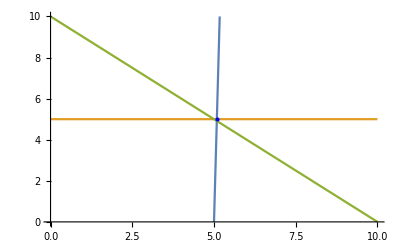

```mathematica
Show[Plot[{p1[x],p2[x], p3[x]},{x,0,10},PlotRange->{0,10}],Graphics[{PointSize[Large],Blue,Point[{solx,soly}]}]]
```

account for tan =0
Add a “cone of confidence.”  Allowing for error in the bearing readings will eventually create a 2-dimmensional confidence interval